# DMDGP Package

```mathematica
(* Put the following two lines at the top of every notebook. *)
(* messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; *)
```

## Instance Creation

### Source Code

```mathematica
ClearAll[GenerateRandomDMDGPInstance];

SetPositionUsingCartesianSystem::usage="Set the atoms positions using atomic rotations and translations.";SetPositionUsingCartesianSystem[d_,t_,w_]:=
Module[
(* declare local variables *)
{a,b,c,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[t[[3]]],d[[3]]Sin[t[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[t[[i]],n];
v=R[v];
(* apply torsion rotation and translation *)
R=RotationTransform[w[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
X
];

SetPositionUsingHomogeneousCoords::usage="Set the atoms positions using internal coordinate system.";
SetPositionUsingHomogeneousCoords[d_,t_,w_]:=
Module[
{B,B1,B2,B3,X,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[t[[3]]],d[[3]]Sin[t[[3]]] ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
{ct,st}={Cos[t[[3]]],Sin[t[[3]]]};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[t[[i]]],Sin[t[[i]]]};
{cw,sw}={Cos[w[[i]]],Sin[w[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
X
];

GenerateRandom3DBackbone::usage="Generates a random backbone in tridimensional Euclidean space.";
GenerateRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords"]:=
Module[
(* declare the local variables *)
{d,t,w,X,output},
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
t=Table[1.91,{i,numberOfAtoms}];
t[[{1,2}]]={0,0};
(* torsion angles *)
w=Table[RandomReal[2Pi],{i,numberOfAtoms}];
w[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=SetPositionUsingHomogeneousCoords[d,t,w],
"CartesianSystem",X=SetPositionUsingCartesianSystem[d,t,w],
_,Throw["InvalidAlgorithm"]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->w,"CovalentBondLengths"->d,"PlaneRotationAngles"->t|>
];

GetMatrixDistance::usage="Gets the complete distance matrix for all coordinates in the array X.";
GetMatrixDistance[x_]:=Table[Norm[x[[i]]-x[[j]]],{i,1,Length[x]},{j,1,Length[x]}];

GenerateRandomDMDGPInstance::usage="Generates a random DMDGP instance.";
GenerateRandomDMDGPInstance[numberOfAtoms_,Dtol_:5.0,algorithm_:"DistanceMatrix"]:=
Module[
(* declare local variables *)
{i,j,k,X,G,D,N,E,output,dij},
X=GenerateRandom3DBackbone[numberOfAtoms];
Switch[algorithm,
"DistanceMatrix",
D=DistanceMatrix[X["Points"]];
G=Table[If[And[0<D[[i]][[j]],D[[i]][[j]]≤Dtol],D[[i]][[j]],Infinity],{i,1,numberOfAtoms},{j,1,numberOfAtoms}];
G=WeightedAdjacencyGraph[G],
"Nearest",
N=Nearest[X["Points"]->Automatic,X["Points"],{All,Dtol}, Method-> "Octree"];
E={};
For[i=1,i≤Length[N],i++,
For[j=1,j≤Length[N[[i]]],j++,
k=N[[i]][[j]];
If[k>i,AppendTo[E,i<->k]]
];
];
G=Graph[E];
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
i=E[[k]][[1]];
j=E[[k]][[2]];
PropertyValue[{G,i<->j},EdgeWeight]=EuclideanDistance[X["Points"][[i]],X["Points"][[j]]]
],
_,Throw["InvalidAlgorithm"]
];
<|"X"->X,"G"->G|>
];

Plot3DBackbone::usage="Plots the points using the coordinates of X[Points].";
Plot3DBackbone[X_]:=Graphics3D[{Line[X["Points"]],{PointSize[Large],Blue,Point[X["Points"]]}}, Axes->True]

CalculateProteinAngles::usage="Calculates the protein angles (plane and torsion) considering the sequence A-B-C-D.";
CalculateProteinAngles[A_,B_,C_,D_]:=
Module[
(* Calculate the plane and torsion angles for X4 *)
{nabc, nbcd},
(* centered at C *)
Print["Angle[BCD] =",N[VectorAngle[B-C,D-C]]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
Print["Angle[ABCD]=",N[VectorAngle[nabc,nbcd]]];
];

CalculateProteinAnglesForAtomAtPosition::usage="Calculates the protein angles (plane and torsion) to i-th atom.";
CalculateProteinAnglesForAtomAtPosition[X_,i_]:=CalculateProteinAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];
```

### Examples

#### Generating Random Backbone

```mathematica
X=GenerateRandom3DBackbone[15];
Print["X=",X];
Plot3DBackbone[X]
```

X=<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.23917,2.25785,-1.01335},{-0.654616,1.32692,-2.07182},{-0.620633,-0.0994652,-1.53057},{-1.89924,-0.827036,-1.93614},{-2.23258,-0.496778,-3.3882},{-1.62522,0.854536,-3.7539},{-0.202532,0.649777,-4.26645},{0.261095,-0.763804,-3.92658},{-0.785998,-1.76874,-4.39814},{-0.0913799,-3.04584,-4.86205},{-0.939407,-3.72442,-5.93399},{-2.39228,-3.78221,-5.47085}},TorsionAngles→{0,0,0,0.78127,0.415961,5.93587,1.61976,0.742235,5.83827,1.54403,6.04157,0.892108,2.54389,3.64138,5.46006},CovalentBondLengths→{0,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91}|>

-Graphics3D-

#### Set Position Using Different Coordinate Systems

```mathematica
d=X["CovalentBondLengths"];
t=X["PlaneRotationAngles"];
w=X["TorsionAngles"];
S=SetPositionUsingCartesianSystem[d,t,w];
P=SetPositionUsingHomogeneousCoords[d,t,w];
Print["S=",S];
Print["P=",P];
CalculateProteinAnglesForAtomAtPosition[S,8];
CalculateProteinAnglesForAtomAtPosition[P,8];
```

S={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.23917,2.25785,-1.01335},{-0.654616,1.32692,-2.07182},{-0.620633,-0.0994652,-1.53057},{-1.89924,-0.827036,-1.93614},{-2.23258,-0.496778,-3.3882},{-1.62522,0.854536,-3.7539},{-0.202532,0.649777,-4.26645},{0.261095,-0.763804,-3.92658},{-0.785998,-1.76874,-4.39814},{-0.0913799,-3.04584,-4.86205},{-0.939407,-3.72442,-5.93399},{-2.39228,-3.78221,-5.47085}}

P={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.23917,2.25785,-1.01335},{-0.654616,1.32692,-2.07182},{-0.620633,-0.0994652,-1.53057},{-1.89924,-0.827036,-1.93614},{-2.23258,-0.496778,-3.3882},{-1.62522,0.854536,-3.7539},{-0.202532,0.649777,-4.26645},{0.261095,-0.763804,-3.92658},{-0.785998,-1.76874,-4.39814},{-0.0913799,-3.04584,-4.86205},{-0.939407,-3.72442,-5.93399},{-2.39228,-3.78221,-5.47085}}

Angle[BCD] =1.91

Angle[ABCD]=0.742235

Angle[BCD] =1.91

Angle[ABCD]=0.742235

#### Generate Random DMDGP Instance

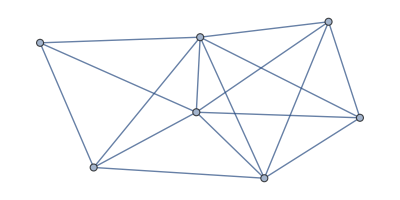
{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
ClearAll[M];
M=GenerateRandomDMDGPInstance[7,Dtol=3.0,algorithm="Nearest"];{G=M["G"],X=M["X"]};
{G,MatrixPlot[GraphDistanceMatrix[G],ColorFunction->"Monochrome"], Plot3DBackbone[X]}
```

#### Timing

```mathematica
(* Comparison between HomogeneousCoords and CartesianSystem algorithms *)
(* 
Print["Time(HomogeneousCoords)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"HomogeneousCoords"]]]]];
Print["Time(CartesianSystem)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"CartesianSystem"]]]]];
*)
```

```mathematica
(* Estimating complexity of random backbone generation *)
(*
Clear[x];
tp=Table[{n,First[Timing[GenerateRandom3DBackbone[n,"HomogeneousCoords"]]]},{n,100,10000,100}];
fp=Fit[tp,{1,x},x];
Show[ListPlot[tp],Plot[{fp},{x,100,10000}],AxesLabel->{HoldForm[Problem Size],HoldForm[Time in Seconds]},PlotLabel->HoldForm[GenerateRandom3DBackbone],LabelStyle->{GrayLevel[0]}]
*)
```

```mathematica
(* Estimating complexity of distance calculation algorithms in GenerateRandomDMDGPInstance function *)
(*
numberOfAtoms=50
First[Timing[M=GenerateRandomDMDGPInstance[numberOfAtoms,Dtol=5.0,algorithm="Nearest"]]]
First[Timing[M=GenerateRandomDMDGPInstance[numberOfAtoms,Dtol=5.0,algorithm="DistanceMatrix"]]]
*)
```

## MDGP Solvers

### Source Code

```mathematica
ClearAll[BPPlotEstimatedComplexity];

GetEdgeWeight::usage="Gets edge weight.";
GetEdgeWeight[G_,E_]:=Module[
{i,D={}},
If[Not[FailureQ[PropertyValue[{G,E[[1]]},EdgeWeight]]],
(* E is a list of edges *)
For[i=1,i≤Length[E],i++,AppendTo[D,PropertyValue[{G,E[[i]]},EdgeWeight]]],
(* E is a single edge *)
D=PropertyValue[{G,E},EdgeWeight]
];
Return[D]
];

IsPositionValid[G_,X_,i_]:=
Module[
(* local variables *)
{j,k,V,Xi,Xj,dij,Dij,errorDij, tolerance=0.001},
(* current position *)
Xi=X[[i]];
(* vertices adjacent to vertex i *)
V= AdjacencyList[G,i];
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]]; 
(* check only the distances to the precedent atoms *)
If[j>i,Continue[]];
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
dij=EuclideanDistance[Xi,Xj];
(* prescribed distance *)
Dij=GetEdgeWeight[G,i<->j];
(* check if actual distance is valid *)
errorDij=Abs[Dij-dij];
If[errorDij≥tolerance,Print["errorDij = ",errorDij];Return[False]]
];
Return[True]
];

IsNaturalOrderValid[G_]:=Module[
(* local variables *)
{i,j},
For[i=4,i≤Length[VertexList[G]],i++,
For[j=1,j≤3,j++,If[FailureQ[GetEdgeWeight[G,i<->(i-j)]],Return[False]]];
];
Return[True]
];

BPGetNodePosition[G_,X_,i_,branch_]:=Module[
{j,u,v,a,b,c,delta,dy,dz,dw,ky,kz,kw,A,x3,y,z,w},
{y,z,w}=Table[X[[i-j]],{j,3}];
{dy,dz,dw}=GetEdgeWeight[G,Table[i<->(i-j),{j,3}]];
{ky,kz,kw}={dy^2-y.y,dz^2-z.z,dw^2-w.w};
(* set x[1:2]=u*x[3]+v *)
A={y[[{1,2}]]-z[[{1,2}]],y[[{1,2}]]-w[[{1,2}]]};
u=LinearSolve[A,{z[[3]]-y[[3]],w[[3]]-y[[3]]}];
v=LinearSolve[A,{(kz-ky)/2,(kw-ky)/2}];
(* set/solve the quadratic equation *)
u={u[[1]],u[[2]],1};v={v[[1]],v[[2]],0};
a=u.u;
b=2*(u.(v-y));
c=v.(v-2*y)-ky;
(* set the free coordinate *)
x3=(-b-Sqrt[b^2-4*a*c])/(2*a);
If[branch==1,x3=(-b/a)-x3];
(* set output *)
u*x3+v
];

BPSolver[G_]:=Module[
(* local variables *)
{i,j,tABC,dAB,dAC,dBC,numberOfAtoms,prune,node,branch,X,S,work},
numberOfAtoms=Length[VertexList[G]];
(* check if natural order is valid *)
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
(* init atoms positions on Euclidean 3d space *)
X=Table[{0,0,0},{i,numberOfAtoms}];
{dAB,dAC,dBC}=GetEdgeWeight[G,{1<->2,1<->3,2<->3}];
(* planar rotation angle for third atom *)
tABC=ArcCos[(dAB^2+dBC^2-dAC^2)/(2*dAB*dBC)];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-dAB,0,0},{-dAB+dBC*Cos[tABC],dBC*Sin[tABC] ,0}};
(* init BPTree *)
{branch=Table[0,{i,numberOfAtoms}],branch[[{1,2,3}]]=1};
{node=3,prune=False};
{work=Table[0,{i,numberOfAtoms}],work[[{1,2,3}]]=1};
(* BP core *)
S={}; (* solutions *)
While[True,
(* go to next node *)
If[prune|| node==numberOfAtoms,
(* if pruned or last node, search for a node to branch *)
i=node; prune=False;
While[i>0,If[branch[[i]]==0,branch[[i]]=1;Break[]];i--];
(* there is no next node *)
If[i==0,Break[]];
(* reset lower (until k) tree levels *)
For[j=i+1,j≤node,j++,branch[[j]]=0];
node=i,
(* if not pruned nor last node, just go to the child node *)
node++
];
(* calculate position of i-th node *)
work[[node]]++;
X[[node]]=BPGetNodePosition[G,X,node,branch[[node]]];
(* prune *)
If[Not[IsPositionValid[G,X,node]],prune=True;Continue[]];
(* new solution found *)
If[node==numberOfAtoms,AppendTo[S,{X,branch}]];
];
Print["A total of ", Length[S]," solutions has been found."];
Return[{S,work}]
];

BPPlotEstimatedComplexity[G_]:=Module[
(* local variables *)
{numberOfAtoms,i,j,k,work,choices,V,R,reduced},
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
numberOfAtoms=Length[VertexList[G]];
{work=Table[1,{i,numberOfAtoms}],work[[4]]=2};
{choices=Table[Infinity,{i,numberOfAtoms}],choices[[{1,2,3,4}]]={1,1,1,2}};
For[i=5,i≤numberOfAtoms,i++,
(* only edges with precedent vertices *)
Print["i=",i];
V=Select[AdjacencyList[G,i],#<i&];
Print["V=",V];
Print["C=",choices[[V]]];
work[[i]]=2*choices[[i-1]];
If[Length[V]<4,
(* there is no additional constraint *)
choices[[i]]=work[[i]],
(* take the four most restrictive constraints *)
R=Table[choices[[V[[j]]]],{j,Length[V]}];
(* minimal number of choices *)
k=RankedMin[R,4];
(* minimal index with minimal number of choices *)
k=Min[Select[V,(choices[[#]]==k)&]];
Print["k=",k," C(k)=",choices[[k]]];
(* update intermediate number of choices *)
For[j=(k+1),j≤i,j++,If[choices[[j]]>choices[[k]],choices[[j]]=choices[[k]]]];
];
];
Print["Estimated number of Solutions ",choices[[numberOfAtoms]],"."];
ListLinePlot[work,Filling->Axis, PlotLegends->{"Estimated"}]
];
```

### Examples

{0.,Null}

A total of 2 solutions has been found.

{0.0625,Null}

Estimated number of Solutions 4.

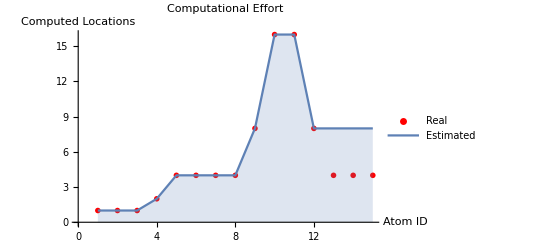

```mathematica
Timing[M=GenerateRandomDMDGPInstance[15,4];]
X=M["X"];
G=M["G"];
Timing[{S,work}=BPSolver[G];]
Show[ListPlot[work,PlotStyle->Red,PlotMarkers->{Automatic,Small},PlotLegends->{"Real"}],BPPlotEstimatedComplexity[G],AxesLabel->{HoldForm[Atom ID],HoldForm[Computed Locations]},PlotLabel->HoldForm[Computational Effort]]
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"TemperatureMap"] *)
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"Monochrome"] *)
```

i=5

V={1,2,3,4}

C={1,1,1,2}

k=4 C(k)=2

i=6

V={2,3,4,5}

C={1,1,2,2}

k=4 C(k)=2

i=7

V={2,4,5,6}

C={1,2,2,2}

k=4 C(k)=2

i=8

V={5,6,7}

C={2,2,2}

i=9

V={6,7,8}

C={2,2,4}

i=10

V={6,7,8,9}

C={2,2,4,8}

k=9 C(k)=8

i=11

V={5,6,7,8,9,10}

C={2,2,2,4,8,8}

k=8 C(k)=4

i=12

V={4,6,9,10,11}

C={2,2,4,4,4}

k=9 C(k)=4

i=13

V={6,10,11,12}

C={2,4,4,4}

k=10 C(k)=4

i=14

V={3,6,8,9,10,11,12,13}

C={1,2,4,4,4,4,4,4}

k=8 C(k)=4

i=15

V={9,10,11,12,13,14}

C={4,4,4,4,4,4}

k=9 C(k)=4

Estimated number of Solutions 4.

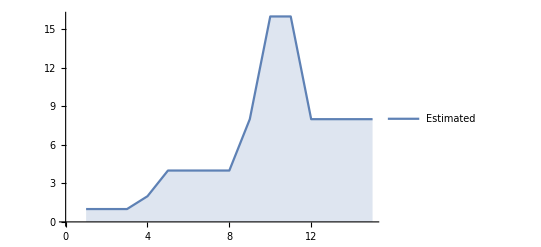

```mathematica
BPPlotEstimatedComplexity[G]
```

```mathematica
i=6
Select[AdjacencyList[G,i],#<i&]
```

```mathematica
Table[S[[i]][[2]],{i,Length[S]}]
```

{{1,1,1,0,1,1,1,1,0,1,0,0,1,0,1},{1,1,1,1,0,0,0,0,1,0,1,1,0,1,0}}

```mathematica
A
t[[1]]++
t
```

A

0

{1,0,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91,1.91}

## BuildUp Solver

### Source Code

```mathematica
BuildUpSolver[G_]:=Module[
{i,j,k,b,d,kmax,A,P,X,Y,U2,U3,U4,V3,V4,numberOfAtoms,maxAbsDetA,absDetA},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* set the position of the first four atoms *)
X[[2]][[1]]=GetEdgeWeight[G,1->2];U2=X[[2]][[1]];
X[[3]][[1]]=(GetEdgeWeight[G,3->1]^2-GetEdgeWeight[G,3->2]^2+U2^2)/(2*U2);U3=X[[3]][[1]];
X[[3]][[2]]=Sqrt[GetEdgeWeight[G,3->1]^2-U3^2];V3=X[[3]][[2]];
X[[4]][[1]]=(GetEdgeWeight[G,4->1]^2-GetEdgeWeight[G,4->2]^2+U2^2)/(2*U2);U4=X[[4]][[1]];
X[[4]][[2]]=(GetEdgeWeight[G,4->2]^2-GetEdgeWeight[G,4->3]^2-(U4-U2)^2+(U4-U3)^2+V3^2)/(2*V3);V4=X[[4]][[2]];
X[[4]][[3]]=Sqrt[GetEdgeWeight[G,4->1]^2-U4^2-V4^2];
(* set remaining atoms *)
For[i=5,i≤numberOfAtoms,i++,
P=AdjacencyList[G,i];
If[Length[P]<4,Throw["NotEnoughAdjacentNodes"]];
P=Permutations[P[[1;;4]]];
(* search for systems with higher statbility *)
maxAbsDetA=0;
For[k=1,k≤Length[P],k++,
Y=Table[X[[P[[k]][[j]]]],{j,4}];
A=2*Table[Y[[1]]-Y[[j]],{j,2,4}];
absDetA=Abs[Det[A]];
If[absDetA>maxAbsDetA,maxAbsDetA=absDetA;kmax=k];
];
(* solve the linear system *)
P=P[[kmax]];
Y=Table[X[[P[[j]]]],{j,4}];
A=Table[Y[[1]]-Y[[j]],{j,2,4}];
d={GetEdgeWeight[G,i->P[[1]]],GetEdgeWeight[G,i->P[[2]]],GetEdgeWeight[G,i->P[[3]]],GetEdgeWeight[G,i->P[[4]]]};
A=2*Table[Y[[1]]-Y[[j]],{j,2,4}];
b=Table[(Norm[Y[[1]]]^2-Norm[Y[[j]]]^2)-(d[[1]]^2-d[[j]]^2),{j,2,4}];
X[[i]]=LinearSolve[A,b];
If[Not[IsPositionValid[G,X,i]],Throw["InvalidSolution on node",i]];
];
Return[X]
];
```

### Example

```mathematica
Timing[M=GenerateRandomDMDGPInstance[500,5];]
X=M["X"];
G=M["G"];
```

{1.76563,Null}

```mathematica
Timing[S=BuildUpSolver[G];]
```

Throw::nocatch: Uncaught Throw[InvalidSolution on node,134] returned to top level.

Hold[Throw[InvalidSolution on node,134]]